## 填充前的Mathematica的相关基础知识

```mathematica
x_               名称为 x 的任意表达式
_h               可代表头部为h的任意表达式
x_h             头部为h、名称为x的任意表达式
```

```mathematica
Head[f[a,b]]
```

f

```mathematica
Head[{a,b,c}]
```

List

```mathematica
Head[45]
```

Integer

```mathematica
Cases[{1,1,f[a],2,3,y,f[8],9,f[10]},_Integer]
```

{1,1,2,3,9}

```mathematica
fig=Plot[x^2,{x,0,1}]//FullForm(*可以看到Plot这个命令里包含Line[],而Line里面是大量的采样点的横纵坐标的集合,命令Line就是把采样点用线段连起来从而画出x^2 的图像,也就是说Plot画图实际上画的其实是一条条直线，只不过它取的点比较密我们分辨不出而已*)
```

Graphics[List[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Line[List[List[2.04082×10^-8,4.16493×10^-16],List[0.000306718,9.40759×10^-8],List[0.000613415,3.76278×10^-7],List[0.000920113,8.46608×10^-7],List[0.00122681,1.50506×10^-6],List[0.00153351,2.35165×10^-6],List[0.00184021,3.38636×10^-6],List[0.0021469,4.60919×10^-6],List[0.0024536,6.02016×10^-6],List[0.0027603,7.61925×10^-6],List[0.003067,9.40646×10^-6],List[0.00337369,0.0000113818],List[0.00368039,0.0000135453],List[0.00398709,0.0000158969],List[0.00429379,0.0000184366],List[0.00490718,0.0000240804],List[0.00521388,0.0000271845],List[0.00552058,0.0000304768],List[0.00613397,0.0000376256],List[0.00644067,0.0000414822],List[0.00674737,0.0000455269],List[0.00736076,0.0000541808],List[0.00766746,0.0000587899],List[0.00797416,0.0000635872],List[0.00858755,0.000073746],List[0.00981434,0.0000963213],List[0.010121,0.000102435],List[0.0104277,0.000108738],List[0.0110411,0.000121907],List[0.0122679,0.000150502],List[0.0125746,0.000158121],List[0.0128813,0.000165928],List[0.0134947,0.000182107],List[0.0147215,0.000216723],List[0.0150282,0.000225847],List[0.0153349,0.000235159],List[0.0159483,0.000254348],List[0.0171751,0.000294983],List[0.0196287,0.000385284],List[0.0199612,0.000398448],List[0.0202937,0.000411832],List[0.0209586,0.000439265],List[0.0222886,0.000496783],List[0.0249486,0.000622432],List[0.0252811,0.000639133],List[0.0256136,0.000656055],List[0.0262786,0.000690563],List[0.0276085,0.000762232],List[0.0302685,0.000916183],List[0.030601,0.000936421],List[0.0309335,0.000956881],List[0.0315985,0.000998465],List[0.0329285,0.00108428],List[0.0355884,0.00126654],List[0.0409084,0.00167349],List[0.0412188,0.00169899],List[0.0415293,0.00172468],List[0.0421502,0.00177664],List[0.043392,0.00188287],List[0.0458757,0.00210458],List[0.0508431,0.00258502],List[0.0511536,0.00261669],List[0.051464,0.00264855],List[0.052085,0.00271284],List[0.0533268,0.00284375],List[0.0558105,0.00311481],List[0.0607779,0.00369395],List[0.0610823,0.00373104],List[0.0613866,0.00376832],List[0.0619954,0.00384343],List[0.0632129,0.00399586],List[0.0656478,0.00430964],List[0.0705178,0.00497276],List[0.0708221,0.00501578],List[0.0711265,0.00505898],List[0.0717353,0.00514595],List[0.0729527,0.0053221],List[0.0753877,0.00568331],List[0.0802576,0.00644129],List[0.0805878,0.0064944],List[0.080918,0.00654772],List[0.0815783,0.00665502],List[0.082899,0.00687224],List[0.0855404,0.00731715],List[0.0908231,0.00824883],List[0.101388,0.0102796],List[0.101697,0.0103422],List[0.102005,0.010405],List[0.102621,0.0105311],List[0.103854,0.0107856],List[0.106319,0.0113037],List[0.111249,0.0123763],List[0.121109,0.0146674],List[0.142481,0.0203008],List[0.163463,0.0267201],List[0.183035,0.0335016],List[0.204257,0.0417211],List[0.22407,0.0502074],List[0.243493,0.0592888],List[0.264567,0.0699956],List[0.284231,0.0807871],List[0.305546,0.0933581],List[0.326471,0.106583],List[0.345986,0.119706],List[0.367151,0.1348],List[0.386907,0.149697],List[0.408314,0.16672],List[0.429331,0.184325],List[0.448938,0.201545],List[0.470196,0.221084],List[0.490044,0.240143],List[0.509502,0.259592],List[0.530611,0.281548],List[0.55031,0.302841],List[0.57166,0.326795],List[0.59262,0.351199],List[0.61217,0.374752],List[0.633371,0.401159],List[0.653162,0.426621],List[0.672563,0.452342],List[0.693616,0.481103],List[0.713258,0.508737],List[0.734551,0.539565],List[0.754434,0.56917],List[0.773927,0.598963],List[0.795071,0.632138],List[0.814805,0.663908],List[0.83619,0.699215],List[0.857186,0.734768],List[0.876771,0.768727],List[0.898007,0.806417],List[0.917833,0.842418],List[0.93727,0.878475],List[0.958357,0.918448],List[0.978034,0.956551],List[0.978378,0.957223],List[0.978721,0.957894],List[0.979407,0.959238],List[0.98078,0.961929],List[0.983526,0.967323],List[0.989017,0.978155],List[0.98936,0.978834],List[0.989704,0.979513],List[0.99039,0.980872],List[0.991763,0.983594],List[0.994509,0.989047],List[0.994852,0.98973],List[0.995195,0.990413],List[0.995881,0.99178],List[0.997254,0.994516],List[0.997597,0.995201],List[0.997941,0.995886],List[0.998627,0.997256],List[0.99897,0.997942],List[0.999314,0.998628],List[0.999657,0.999314],List[1.,1.]]]],"Charting`Private`Tag$30708#1"]]],List[]],List[Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[0,1],List[0.,1.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.02]]]],Rule[Ticks,List[Automatic,Automatic]]]]

```mathematica
Cases[fig,l_Line:>First@l,Infinity]//FullForm(*运用模式匹配把fig里面的所有Line[]挑出来(这里只要一条曲线x^2),而命令First会把外层的Line脱去,从而只剩一系列点集,如{{x0,y0},{x1,y1},{x2,y2},{x3,y3}}*)
```

List[List[List[2.04082×10^-8,4.16493×10^-16],List[0.000306718,9.40759×10^-8],List[0.000613415,3.76278×10^-7],List[0.000920113,8.46608×10^-7],List[0.00122681,1.50506×10^-6],List[0.00153351,2.35165×10^-6],List[0.00184021,3.38636×10^-6],List[0.0021469,4.60919×10^-6],List[0.0024536,6.02016×10^-6],List[0.0027603,7.61925×10^-6],List[0.003067,9.40646×10^-6],List[0.00337369,0.0000113818],List[0.00368039,0.0000135453],List[0.00398709,0.0000158969],List[0.00429379,0.0000184366],List[0.00490718,0.0000240804],List[0.00521388,0.0000271845],List[0.00552058,0.0000304768],List[0.00613397,0.0000376256],List[0.00644067,0.0000414822],List[0.00674737,0.0000455269],List[0.00736076,0.0000541808],List[0.00766746,0.0000587899],List[0.00797416,0.0000635872],List[0.00858755,0.000073746],List[0.00981434,0.0000963213],List[0.010121,0.000102435],List[0.0104277,0.000108738],List[0.0110411,0.000121907],List[0.0122679,0.000150502],List[0.0125746,0.000158121],List[0.0128813,0.000165928],List[0.0134947,0.000182107],List[0.0147215,0.000216723],List[0.0150282,0.000225847],List[0.0153349,0.000235159],List[0.0159483,0.000254348],List[0.0171751,0.000294983],List[0.0196287,0.000385284],List[0.0199612,0.000398448],List[0.0202937,0.000411832],List[0.0209586,0.000439265],List[0.0222886,0.000496783],List[0.0249486,0.000622432],List[0.0252811,0.000639133],List[0.0256136,0.000656055],List[0.0262786,0.000690563],List[0.0276085,0.000762232],List[0.0302685,0.000916183],List[0.030601,0.000936421],List[0.0309335,0.000956881],List[0.0315985,0.000998465],List[0.0329285,0.00108428],List[0.0355884,0.00126654],List[0.0409084,0.00167349],List[0.0412188,0.00169899],List[0.0415293,0.00172468],List[0.0421502,0.00177664],List[0.043392,0.00188287],List[0.0458757,0.00210458],List[0.0508431,0.00258502],List[0.0511536,0.00261669],List[0.051464,0.00264855],List[0.052085,0.00271284],List[0.0533268,0.00284375],List[0.0558105,0.00311481],List[0.0607779,0.00369395],List[0.0610823,0.00373104],List[0.0613866,0.00376832],List[0.0619954,0.00384343],List[0.0632129,0.00399586],List[0.0656478,0.00430964],List[0.0705178,0.00497276],List[0.0708221,0.00501578],List[0.0711265,0.00505898],List[0.0717353,0.00514595],List[0.0729527,0.0053221],List[0.0753877,0.00568331],List[0.0802576,0.00644129],List[0.0805878,0.0064944],List[0.080918,0.00654772],List[0.0815783,0.00665502],List[0.082899,0.00687224],List[0.0855404,0.00731715],List[0.0908231,0.00824883],List[0.101388,0.0102796],List[0.101697,0.0103422],List[0.102005,0.010405],List[0.102621,0.0105311],List[0.103854,0.0107856],List[0.106319,0.0113037],List[0.111249,0.0123763],List[0.121109,0.0146674],List[0.142481,0.0203008],List[0.163463,0.0267201],List[0.183035,0.0335016],List[0.204257,0.0417211],List[0.22407,0.0502074],List[0.243493,0.0592888],List[0.264567,0.0699956],List[0.284231,0.0807871],List[0.305546,0.0933581],List[0.326471,0.106583],List[0.345986,0.119706],List[0.367151,0.1348],List[0.386907,0.149697],List[0.408314,0.16672],List[0.429331,0.184325],List[0.448938,0.201545],List[0.470196,0.221084],List[0.490044,0.240143],List[0.509502,0.259592],List[0.530611,0.281548],List[0.55031,0.302841],List[0.57166,0.326795],List[0.59262,0.351199],List[0.61217,0.374752],List[0.633371,0.401159],List[0.653162,0.426621],List[0.672563,0.452342],List[0.693616,0.481103],List[0.713258,0.508737],List[0.734551,0.539565],List[0.754434,0.56917],List[0.773927,0.598963],List[0.795071,0.632138],List[0.814805,0.663908],List[0.83619,0.699215],List[0.857186,0.734768],List[0.876771,0.768727],List[0.898007,0.806417],List[0.917833,0.842418],List[0.93727,0.878475],List[0.958357,0.918448],List[0.978034,0.956551],List[0.978378,0.957223],List[0.978721,0.957894],List[0.979407,0.959238],List[0.98078,0.961929],List[0.983526,0.967323],List[0.989017,0.978155],List[0.98936,0.978834],List[0.989704,0.979513],List[0.99039,0.980872],List[0.991763,0.983594],List[0.994509,0.989047],List[0.994852,0.98973],List[0.995195,0.990413],List[0.995881,0.99178],List[0.997254,0.994516],List[0.997597,0.995201],List[0.997941,0.995886],List[0.998627,0.997256],List[0.99897,0.997942],List[0.999314,0.998628],List[0.999657,0.999314],List[1.,1.]]]

## Example1---利用多边形填充方法填充任意两条曲线

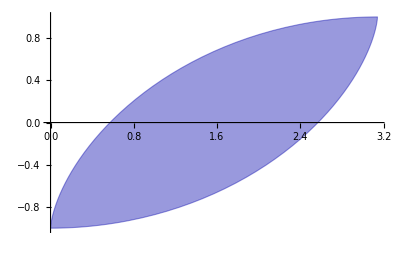

```mathematica
plot=ParametricPlot[{{u+Sin[u],-Cos[u]},{u+Sin[u+Pi],Cos[u+Pi]}},{u,0,Pi},Axes->True];
{line1,line2}=Cases[plot,l_Line:>First@l,Infinity];
Graphics[{Opacity[0.4],Darker@Blue,EdgeForm[Darker@Blue],Polygon[Join[line1,Reverse@line2]]},Options[plot]]
```

## Example2---应用于黑洞阴影

```mathematica
Δ[a_,r_]:=r^2-2r+a^2+0.02;
ξ[a_,r_]:=((1+0.02)*(a^2+r*(0.02-r))+r*Δ[a,r])/(a*(1-r+0.02));
η[a_,r_]:=r^2/(a^2*(1-r+0.02)^2)*(4r*(1+0.02)*(a^2+0.02*1.02)-4*0.02*1.02*Δ[a,r]-r^2*(r-3*1.02)^2);
```

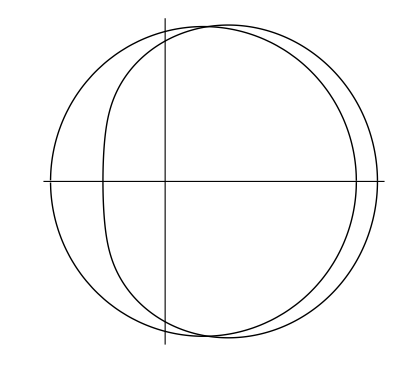

```mathematica
aa=ParametricPlot[{{-ξ[0.99,r],√η[0.99,r]},{-ξ[0.99,r],-√η[0.99,r]}},{r,1,5},PlotPoints->500,PlotStyle->{Directive[Thin,Black],Directive[Thin,Black]},Ticks->None];
bb=ParametricPlot[{{-ξ[0.2,r],√η[0.2,r]},{-ξ[0.2,r],-√η[0.2,r]}},{r,1,10},PlotPoints->500,PlotStyle->{Directive[Thin,Black],Directive[Thin,Black]},Ticks->None];
Show[aa,bb,PlotRange->All]
```

```mathematica
{curve1,curve2}=Cases[aa,l_Line:>First@l,Infinity];
{curve3,curve4}=Cases[bb,l_Line:>First@l,Infinity];
Show[aa,bb,Graphics[{Opacity[0.4],Darker@Blue,Polygon[Join[Reverse@curve4,curve3]->Join[Reverse@curve2,curve1]]}],Graphics[{Opacity[0.4],Darker@Blue,Polygon[Join[Reverse@curve2,curve1]->Join[Reverse@curve4,curve3]]}],PlotRange->All]
```

-Graphics-

## Example3---模式匹配Cases的其他应用: 交换坐标轴、反转拉伸图像

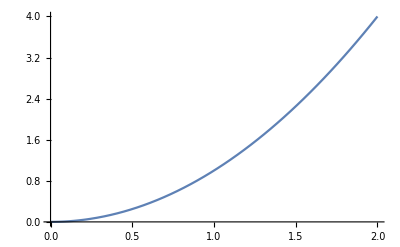

```mathematica
fig=Plot[x^2,{x,0,2}]
```

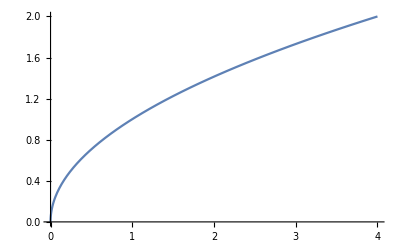

```mathematica
data=First@Cases[fig,l_Line:>First@l,Infinity];
ListLinePlot[Reverse[data,2]]
```

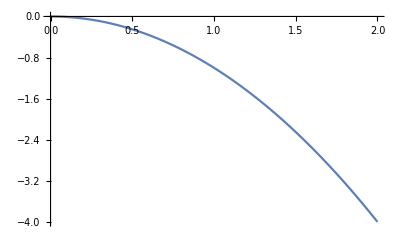

```mathematica
xx=First@Transpose@data;
yy=-Last@Transpose@data;
ListLinePlot[Thread[{xx,yy}]]
```